## ShowOutwardNormals-example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (3.0.51f (14 June 2017)) loaded Wed 14 Jun 2017 12:53:38
using xCellerator 0.95 and XSSA 1.3.2
GPL License Terms Apply

```mathematica
poly={{0,0}, {1,0}, {5,1}, {1, 3}};
```

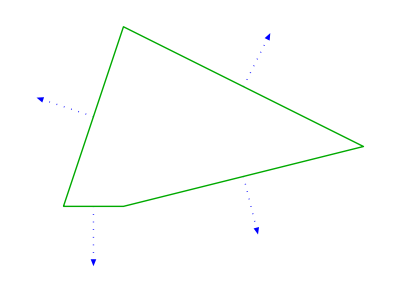

```mathematica
arrows=ShowOutwardNormals[poly, {Blue, Dotted, Thick}, False];
border=Boundary[poly, {Darker[Green], Thick}];
Show[arrows, border]
```

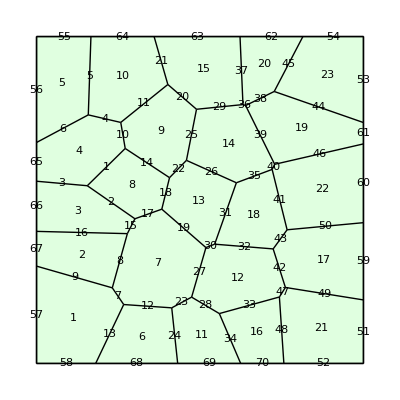

```mathematica
T=TemplateRandomSquareGrid[25,{0,0}, {10,10}];
ShowTissue[T, "CellNumbers"-> True, "EdgeNumbers"-> True]
```

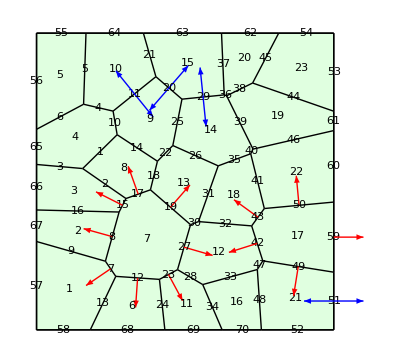

```mathematica
Show[ShowTissue[T, "CellNumbers"-> True, "EdgeNumbers"-> True],

ShowOutwardNormals[T, "Cells"-> {7,17}, "Style"-> Red],

ShowOutwardNormals[T, "Edges"-> {11,20,29,51}, "Style"-> Blue]
]
```